```mathematica
Clear[rwin, rdie, rrun, rwait, ph]
```

```mathematica
(*rwin = 50
rdie = -100
rrun = 0
rwait = -10*)
```

```mathematica
ph[vrun_, vwin_, vinjury_, vwait_] := (0.5*vwin-vwait)/(vrun-vwait-0.5vinjury)
```

```mathematica
ph2[crun_, vwin_, cinjury_, cwait_] := ph[-crun, vwin, -cinjury, -cwait]
```

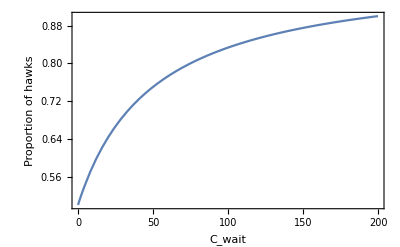

```mathematica
cwaitGraph = Plot[ph2[crun, vwin, cinjury, cwait]/.{vwin-> 50,cinjury-> 100, crun->0}, {cwait, 0,200}, Frame->True, FrameLabel-> {"C_wait", "Proportion of hawks"}, LabelStyle->{16, Black}]
```

```mathematica
dir = NotebookDirectory[]
```

C:\Users\chris\Documents\Code\personalProblems\

```mathematica
Export[StringJoin[dir,"cwaitGraph.jpg"], cwaitGraph]
```

C:\Users\chris\Documents\Code\personalProblems\cwaitGraph.jpg

```mathematica
ph3[crun_, cinjury_, cwait_] := (0.5+cwait)/(crun+cwait+0.5cinjury)
```

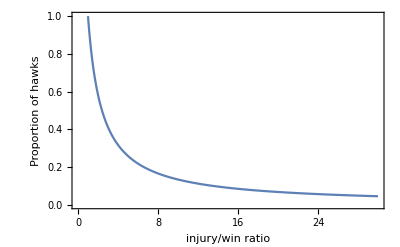

```mathematica
ratGraph = Plot[ph3[crun, cinjury, cwait]/.{crun->0, cwait->1/5}, {cinjury, 0,30}, Frame->True, FrameLabel-> {"injury/win ratio", "Proportion of hawks"}, LabelStyle->{16, Black}, PlotRange->{{0,30},{0,1}}]
```

```mathematica
Export[StringJoin[dir,"ratGraph.jpg"], ratGraph]
```

C:\Users\chris\Documents\Code\personalProblems\ratGraph.jpg